```mathematica
Clear["Global`*"]
```

## Initial Value

```mathematica
L=80;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

## Product Random NRZ Signal

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

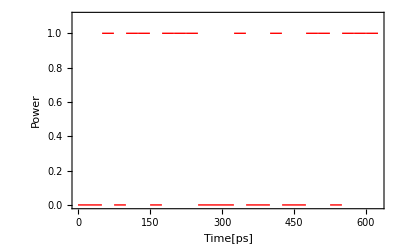

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

```mathematica
∫_0^(bit*25*10^-12) signal[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1
```

-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))

```mathematica
fc[f_]:=-1/(2 f π)ⅈ ⅇ^(-(ⅈ f π)/800000000) (-1+ⅇ^((ⅈ f π)/20000000000)) (1+ⅇ^((ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/10000000000)+ⅇ^((ⅈ f π)/5000000000)+ⅇ^((ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/2500000000)+ⅇ^((11 ⅈ f π)/20000000000)+ⅇ^((3 ⅈ f π)/4000000000)+ⅇ^((ⅈ f π)/1250000000)+ⅇ^((17 ⅈ f π)/20000000000)+ⅇ^((19 ⅈ f π)/20000000000)+ⅇ^((ⅈ f π)/1000000000)+ⅇ^((11 ⅈ f π)/10000000000))
```

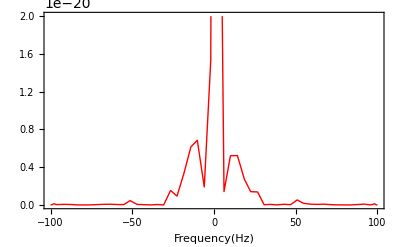

```mathematica
Plot[(Re[fc[f*10^9]]^2+Im[fc[f*10^9]]^2),{f,-100,100},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15},PlotRange->{0,20*10^-21}]
```

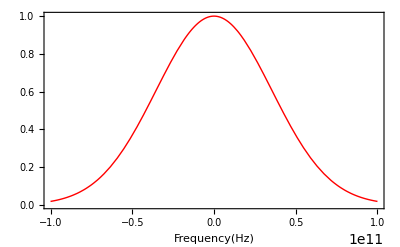

```mathematica
mado[f_]:=ⅇ^(-(f*10^-10.7)^2)
Plot[mado[f],{f,-100*10^9,100*10^9},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Frequency(Hz)",},BaseStyle->{Bold,FontSize->15}]
```

```mathematica
For[i=1,i≤1200,i++,sinsper1[i]=Re[fc[i*10^8]]*mado[i*10^8]]       
For[i=1,i≤1200,i++,sinspei1[i]=Im[fc[i*10^8]]*mado[i*10^8]]       
sig[t_]:=sig[t]=(∑_(i=1)^1200 sinsper1[i]*Cos[2*Pi*i*10^8*t]+∑_(i=1)^1200 sinspei1[i]*Sin[-2*Pi*i*10^8*t])
```

```mathematica
minnrz=-MinValue[sig[x1*10^-12],x1];
maxnrz=MaxValue[sig[x]+minnrz,x];
nrzsig[t_]:=(sig[t]+minnrz)/maxnrz;
```

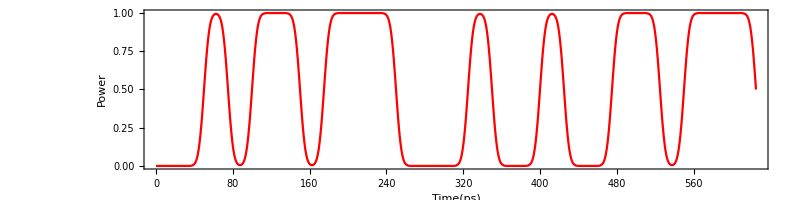

```mathematica
Plot[nrzsig[t*10^-12],{t,0,bit*25},Frame->True,FrameLabel->{"Time(ps)","Power"},PlotStyle->{Red},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Function for Compensation Fiber Dispersion

```mathematica
f[x_]:=1/(√(2*Pi*β2*80))*10^6*Exp[+ⅈ*(((t[x]*10^-3)^2)/(2*β2*80)-Pi/4)];
```

```mathematica
FindMaximum[{Re@f[x1],{0<x1<10}},{x1,3}]
```

{9.87697×10^15,{x1→2.4694}}

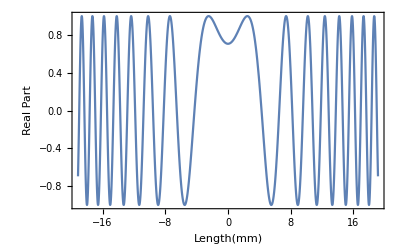

```mathematica
max=9.87972350691273*^15;
Plot[Re@f[l]/max,{l,-electrodelengthmm/2,electrodelengthmm/2},Frame->True,FrameLabel->{"Length(mm)","Real Part"}]
```

## Impulse Responce for Fiber Dispersion

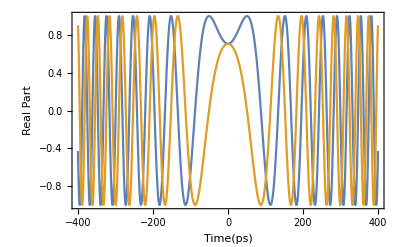

```mathematica
hdis[t_]:=(*1/(√(2*Pi*β2*L))*10^6**)Exp[-ⅈ*(t^2/(2*β2*L)-Pi/4)];(*Impluse ver.time*)
(*FindMaximum[{Re@hdis[x1],{0<x1<10}},{x1,3}]
max=9.876974769287008*^15;*)
Plot[{Re@hdis[t*10^-12],Im@hdis[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Impulse Responce for CompensationDispersion

```mathematica
hcmp[t_]:=
(*1/(√(2*Pi*β2*80))*10^6*)Exp[+ⅈ*(t^2/(2*β2*80)-Pi/4)];
```

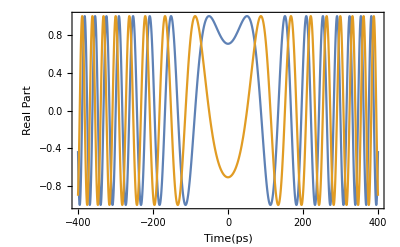

```mathematica
Plot[{Re@hcmp[t*10^-12],Im@hcmp[t*10^-12]},{t,-400,400},Frame->True,FrameLabel->{"Time(ps)","Real Part"}]
```

## Sampling

```mathematica
samp=0.5;(*sampling number*)
```

```mathematica
bound=IntegerPart[total*10^12];
```

```mathematica
For[i=-100000,i≤-bound/2,i=i+samp,hcmp2[i]=0]
For[j=0;i=-bound/2,i≤bound/2,i=i+samp;j=j+samp,hcmp2[i]=hcmp[j*10^-12]]
For[i=bound/2,i≤100000,i=i+samp,hcmp2[i]=0]
```

```mathematica
IntegerPart[total*10^12]
```

784

```mathematica
For[i=-100.,i≤bit*25+100,i=i+samp,
nrzsig2[i]=nrzsig[i*10^-12];If[Mod[i,500]==0,Print[i]]]
```

0.

500.

```mathematica
For[i=-100000,i≤-400,i=i+samp,hcmp3[i]=0]
For[i=-400,i≤400,i=i+samp,hcmp3[i]=hcmp[i*10^-12]]
For[i=400,i≤100000,i=i+samp,hcmp3[i]=0]
```

```mathematica
For[i=-100000,i≤100000,i=i+samp,hdis2[i]=hdis[i*10^-12]]
```

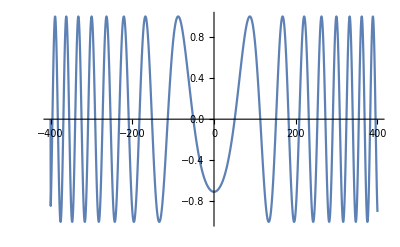

```mathematica
ListLinePlot[Table[{m,Im@hcmp3[m]},{m,-400,400,samp}]]
```

## Simulation

```mathematica
simu0[a_]:=simu0[a]=Sum[hdis2[z]*hcmp3[a-z],{z,-10000,10000,samp}]
simu1[a_]:=simu1[a]=Sum[nrzsig2[t]*simu0[a-t],{t,-100,25*bit+100,samp}]
```

```mathematica
simu1[-100.]
```

589.996+183.268 ⅈ

```mathematica
For[i=-100.,i≤25*bit+100,i=i+samp,after[i]=simu1[i];If[Mod[i,50]==0,Print[i]]]
```

-100.

-50.

0.

50.

100.

150.

200.

250.

300.

350.

400.

450.

500.

550.

600.

650.

700.

```mathematica
aftersig=Table[{m,Abs[after[m]]},{m,-100,25*bit+100,samp}]
```

{{-100.,617.804},{-99.5,585.684},{-99.,552.016},{-98.5,517.103},{-98.,481.295},{-97.5,444.984},{-97.,408.589},{-96.5,372.558},{-96.,337.349},{-95.5,303.43},{-95.,271.255},{-94.5,241.254},{-94.,213.796},{-93.5,189.162},{-93.,167.487},{-92.5,148.715},{-92.,132.563},{-91.5,118.527},{-91.,105.95},{-90.5,94.1609},{-90.,82.6591},{-89.5,71.3871},{-89.,61.1828},{-88.5,54.495},{-88.,55.3707},{-87.5,66.2958},{-87.,85.8065},{-86.5,111.267},{-86.,140.806},{-85.5,173.219},{-85.,207.628},{-84.5,243.288},{-84.,279.507},{-83.5,315.617},{-83.,350.967},{-82.5,384.922},{-82.,416.874},{-81.5,446.253},{-81.,472.537},{-80.5,495.269},{-80.,514.063},{-79.5,528.622},{-79.,538.744},{-78.5,544.334},{-78.,545.408},{-77.5,542.104},{-77.,534.687},{-76.5,523.545},{-76.,509.197},{-75.5,492.289},{-75.,473.582},{-74.5,453.943},{-74.,434.314},{-73.5,415.665},{-73.,398.93},{-72.5,384.905},{-72.,374.146},{-71.5,366.869},{-71.,362.896},{-70.5,361.67},{-70.,362.336},{-69.5,363.856},{-69.,365.134},{-68.5,365.107},{-68.,362.815},{-67.5,357.435},{-67.,348.303},{-66.5,334.92},{-66.,316.965},{-65.5,294.319},{-65.,267.109},{-64.5,235.828},{-64.,201.605},{-63.5,166.878},{-63.,137.018},{-62.5,122.61},{-62.,134.984},{-61.5,172.706},{-61.,226.169},{-60.5,288.476},{-60.,355.942},{-59.5,426.424},{-59.,498.442},{-58.5,570.819},{-58.,642.539},{-57.5,712.683},{-57.,780.416},{-56.5,844.978},{-56.,905.695},{-55.5,961.985},{-55.,1013.37},{-54.5,1059.49},{-54.,1100.1},{-53.5,1135.09},{-53.,1164.49},{-52.5,1188.44},{-52.,1207.24},{-51.5,1221.28},{-51.,1231.07},{-50.5,1237.2},{-50.,1240.31},{-49.5,1241.08},{-49.,1240.19},{-48.5,1238.26},{-48.,1235.87},{-47.5,1233.44},{-47.,1231.3},{-46.5,1229.6},{-46.,1228.31},{-45.5,1227.28},{-45.,1226.17},{-44.5,1224.54},{-44.,1221.84},{-43.5,1217.49},{-43.,1210.85},{-42.5,1201.32},{-42.,1188.32},{-41.5,1171.36},{-41.,1150.04},{-40.5,1124.08},{-40.,1093.33},{-39.5,1057.82},{-39.,1017.76},{-38.5,973.521},{-38.,925.738},{-37.5,875.266},{-37.,823.235},{-36.5,771.077},{-36.,720.545},{-35.5,673.71},{-35.,632.898},{-34.5,600.503},{-34.,578.655},{-33.5,568.752},{-33.,571.066},{-32.5,584.624},{-32.,607.481},{-31.5,637.21},{-31.,671.364},{-30.5,707.788},{-30.,744.743},{-29.5,780.939},{-29.,815.497},{-28.5,847.908},{-28.,877.97},{-27.5,905.731},{-27.,931.438},{-26.5,955.471},{-26.,978.289},{-25.5,1000.37},{-25.,1022.14},{-24.5,1043.97},{-24.,1066.06},{-23.5,1088.48},{-23.,1111.16},{-22.5,1133.84},{-22.,1156.16},{-21.5,1177.63},{-21.,1197.72},{-20.5,1215.89},{-20.,1231.58},{-19.5,1244.31},{-19.,1253.68},{-18.5,1259.38},{-18.,1261.24},{-17.5,1259.23},{-17.,1253.44},{-16.5,1244.15},{-16.,1231.77},{-15.5,1216.84},{-15.,1200.03},{-14.5,1182.15},{-14.,1164.03},{-13.5,1146.57},{-13.,1130.65},{-12.5,1117.08},{-12.,1106.54},{-11.5,1099.53},{-11.,1096.33},{-10.5,1096.97},{-10.,1101.24},{-9.5,1108.72},{-9.,1118.79},{-8.5,1130.77},{-8.,1143.89},{-7.5,1157.39},{-7.,1170.59},{-6.5,1182.89},{-6.,1193.82},{-5.5,1203.04},{-5.,1210.38},{-4.5,1215.79},{-4.,1219.38},{-3.5,1221.37},{-3.,1222.09},{-2.5,1221.93},{-2.,1221.34},{-1.5,1220.78},{-1.,1220.67},{-0.5,1221.4},{0.,1223.24},{0.5,1226.38},{1.,1230.88},{1.5,1236.67},{2.,1243.56},{2.5,1251.26},{3.,1259.37},{3.5,1267.45},{4.,1274.99},{4.5,1281.49},{5.,1286.45},{5.5,1289.35},{6.,1289.75},{6.5,1287.22},{7.,1281.38},{7.5,1271.91},{8.,1258.51},{8.5,1240.97},{9.,1219.09},{9.5,1192.76},{10.,1161.88},{10.5,1126.44},{11.,1086.45},{11.5,1042.02},{12.,993.298},{12.5,940.513},{13.,883.982},{13.5,824.116},{14.,761.437},{14.5,696.602},{15.,630.43},{15.5,563.948},{16.,498.462},{16.5,435.654},{17.,377.729},{17.5,327.544},{18.,288.547},{18.5,264.036},{19.,255.446},{19.5,260.792},{20.,275.263},{20.5,293.37},{21.,310.44},{21.5,322.942},{22.,328.274},{22.5,324.503},{23.,310.176},{23.5,284.214},{24.,245.867},{24.5,194.752},{25.,131.148},{25.5,59.0614},{26.,55.6685},{26.5,152.193},{27.,266.976},{27.5,393.762},{28.,530.625},{28.5,675.859},{29.,827.614},{29.5,983.827},{30.,1142.22},{30.5,1300.29},{31.,1455.35},{31.5,1604.55},{32.,1744.88},{32.5,1873.2},{33.,1986.31},{33.5,2080.94},{34.,2153.82},{34.5,2201.72},{35.,2221.48},{35.5,2210.11},{36.,2164.82},{36.5,2083.21},{37.,1963.45},{37.5,1804.65},{38.,1607.77},{38.5,1377.6},{39.,1128.43},{39.5,900.503},{40.,794.976},{40.5,938.636},{41.,1313.55},{41.5,1831.62},{42.,2445.45},{42.5,3135.57},{43.,3893.16},{43.5,4713.36},{44.,5592.82},{44.5,6528.75},{45.,7518.44},{45.5,8559.12},{46.,9647.81},{46.5,10781.3},{47.,11956.},{47.5,13168.1},{48.,14413.7},{48.5,15688.2},{49.,16987.2},{49.5,18305.7},{50.,19638.7},{50.5,20981.},{51.,22327.},{51.5,23671.3},{52.,25008.2},{52.5,26331.9},{53.,27636.8},{53.5,28916.9},{54.,30166.7},{54.5,31380.4},{55.,32552.6},{55.5,33677.8},{56.,34750.9},{56.5,35766.8},{57.,36720.9},{57.5,37608.6},{58.,38425.9},{58.5,39169.},{59.,39834.3},{59.5,40418.8},{60.,40919.9},{60.5,41335.2},{61.,41662.9},{61.5,41901.4},{62.,42049.8},{62.5,42107.4},{63.,42073.8},{63.5,41949.4},{64.,41734.5},{64.5,41430.2},{65.,41037.6},{65.5,40558.5},{66.,39994.8},{66.5,39348.7},{67.,38622.9},{67.5,37820.3},{68.,36944.1},{68.5,35997.8},{69.,34985.2},{69.5,33910.3},{70.,32777.4},{70.5,31591.},{71.,30356.},{71.5,29077.2},{72.,27759.8},{72.5,26409.3},{73.,25031.1},{73.5,23630.9},{74.,22214.5},{74.5,20787.7},{75.,19356.4},{75.5,17926.7},{76.,16504.4},{76.5,15095.4},{77.,13705.6},{77.5,12340.6},{78.,11006.3},{78.5,9707.83},{79.,8450.62},{79.5,7239.66},{80.,6079.77},{80.5,4975.5},{81.,3931.11},{81.5,2950.59},{82.,2037.63},{82.5,1195.61},{83.,427.758},{83.5,264.777},{84.,876.664},{84.5,1407.8},{85.,1856.1},{85.5,2220.11},{86.,2498.77},{86.5,2691.33},{87.,2797.43},{87.5,2817.06},{88.,2750.7},{88.5,2599.39},{89.,2365.07},{89.5,2051.31},{90.,1665.55},{90.5,1227.38},{91.,809.91},{91.5,711.174},{92.,1169.05},{92.5,1889.85},{93.,2733.01},{93.5,3663.13},{94.,4666.89},{94.5,5736.65},{95.,6866.52},{95.5,8051.18},{96.,9285.4},{96.5,10563.9},{97.,11881.2},{97.5,13231.7},{98.,14609.5},{98.5,16008.7},{99.,17423.1},{99.5,18846.5},{100.,20272.4},{100.5,21694.6},{101.,23106.7},{101.5,24502.5},{102.,25875.8},{102.5,27220.7},{103.,28531.4},{103.5,29802.7},{104.,31029.4},{104.5,32207.},{105.,33331.1},{105.5,34398.2},{106.,35404.9},{106.5,36348.6},{107.,37227.},{107.5,38038.7},{108.,38782.5},{108.5,39457.8},{109.,40064.7},{109.5,40603.7},{110.,41075.7},{110.5,41482.1},{111.,41824.8},{111.5,42105.9},{112.,42328.1},{112.5,42494.2},{113.,42607.3},{113.5,42670.8},{114.,42688.3},{114.5,42663.5},{115.,42600.2},{115.5,42502.5},{116.,42374.4},{116.5,42219.8},{117.,42043.},{117.5,41848.},{118.,41638.8},{118.5,41419.3},{119.,41193.5},{119.5,40964.9},{120.,40737.1},{120.5,40513.6},{121.,40297.5},{121.5,40091.7},{122.,39899.},{122.5,39721.6},{123.,39561.6},{123.5,39420.9},{124.,39300.9},{124.5,39202.6},{125.,39126.7},{125.5,39073.7},{126.,39043.4},{126.5,39035.4},{127.,39049.1},{127.5,39083.2},{128.,39136.4},{128.5,39206.8},{129.,39292.4},{129.5,39390.7},{130.,39499.1},{130.5,39614.7},{131.,39734.4},{131.5,39854.9},{132.,39972.9},{132.5,40084.6},{133.,40186.7},{133.5,40275.3},{134.,40346.7},{134.5,40397.3},{135.,40423.4},{135.5,40421.5},{136.,40388.},{136.5,40319.6},{137.,40213.1},{137.5,40065.3},{138.,39873.4},{138.5,39634.8},{139.,39346.9},{139.5,39007.5},{140.,38614.8},{140.5,38166.9},{141.,37662.4},{141.5,37100.3},{142.,36479.6},{142.5,35799.9},{143.,35061.},{143.5,34263.},{144.,33406.5},{144.5,32492.4},{145.,31521.9},{145.5,30496.6},{146.,29418.8},{146.5,28290.7},{147.,27115.3},{147.5,25896.},{148.,24636.3},{148.5,23340.4},{149.,22012.9},{149.5,20658.6},{150.,19282.8},{150.5,17891.1},{151.,16489.5},{151.5,15084.1},{152.,13681.5},{152.5,12288.2},{153.,10911.3},{153.5,9557.67},{154.,8234.69},{154.5,6949.82},{155.,5711.},{155.5,4527.19},{156.,3409.84},{156.5,2378.06},{157.,1480.74},{157.5,911.004},{158.,1071.14},{158.5,1651.04},{159.,2271.35},{159.5,2839.58},{160.,3329.94},{160.5,3731.97},{161.,4040.26},{161.5,4251.77},{162.,4364.83},{162.5,4378.91},{163.,4294.43},{163.5,4112.92},{164.,3837.2},{164.5,3472.03},{165.,3025.51},{165.5,2513.},{166.,1968.79},{166.5,1485.41},{167.,1303.6},{167.5,1661.77},{168.,2408.72},{168.5,3349.92},{169.,4405.04},{169.5,5541.09},{170.,6740.68},{170.5,7992.16},{171.,9286.28},{171.5,10615.},{172.,11970.7},{172.5,13346.3},{173.,14735.},{173.5,16130.1},{174.,17525.4},{174.5,18914.5},{175.,20291.8},{175.5,21651.6},{176.,22988.7},{176.5,24298.3},{177.,25575.7},{177.5,26816.9},{178.,28018.},{178.5,29175.8},{179.,30287.3},{179.5,31349.9},{180.,32361.5},{180.5,33320.3},{181.,34225.},{181.5,35074.5},{182.,35868.2},{182.5,36605.8},{183.,37287.3},{183.5,37913.},{184.,38483.4},{184.5,38999.5},{185.,39462.3},{185.5,39873.1},{186.,40233.7},{186.5,40545.6},{187.,40811.},{187.5,41031.9},{188.,41210.6},{188.5,41349.6},{189.,41451.5},{189.5,41519.1},{190.,41555.2},{190.5,41562.7},{191.,41544.6},{191.5,41504.},{192.,41444.},{192.5,41367.8},{193.,41278.4},{193.5,41179.},{194.,41072.5},{194.5,40961.9},{195.,40850.},{195.5,40739.5},{196.,40632.9},{196.5,40532.5},{197.,40440.5},{197.5,40358.7},{198.,40288.7},{198.5,40231.9},{199.,40189.2},{199.5,40161.4},{200.,40148.8},{200.5,40151.5},{201.,40169.3},{201.5,40201.4},{202.,40247.1},{202.5,40305.},{203.,40373.5},{203.5,40451.},{204.,40535.5},{204.5,40624.6},{205.,40716.2},{205.5,40807.7},{206.,40896.6},{206.5,40980.5},{207.,41056.9},{207.5,41123.5},{208.,41178.1},{208.5,41218.8},{209.,41243.7},{209.5,41251.4},{210.,41240.8},{210.5,41211.},{211.,41161.4},{211.5,41092.},{212.,41003.},{212.5,40894.9},{213.,40768.7},{213.5,40625.5},{214.,40467.},{214.5,40295.},{215.,40111.5},{215.5,39918.8},{216.,39719.5},{216.5,39516.1},{217.,39311.4},{217.5,39108.2},{218.,38909.3},{218.5,38717.5},{219.,38535.6},{219.5,38366.2},{220.,38212.},{220.5,38075.2},{221.,37958.3},{221.5,37863.1},{222.,37791.5},{222.5,37745.},{223.,37724.9},{223.5,37732.},{224.,37767.},{224.5,37830.3},{225.,37921.7},{225.5,38041.},{226.,38187.2},{226.5,38359.3},{227.,38555.8},{227.5,38774.9},{228.,39014.3},{228.5,39271.5},{229.,39543.7},{229.5,39827.5},{230.,40119.6},{230.5,40416.1},{231.,40713.1},{231.5,41006.2},{232.,41291.2},{232.5,41563.4},{233.,41818.2},{233.5,42050.9},{234.,42256.7},{234.5,42430.9},{235.,42569.},{235.5,42666.3},{236.,42718.7},{236.5,42721.8},{237.,42671.8},{237.5,42565.1},{238.,42398.4},{238.5,42168.8},{239.,41873.7},{239.5,41510.9},{240.,41078.9},{240.5,40576.2},{241.,40002.3},{241.5,39356.7},{242.,38639.8},{242.5,37852.2},{243.,36995.2},{243.5,36070.6},{244.,35080.5},{244.5,34027.7},{245.,32915.5},{245.5,31747.6},{246.,30528.1},{246.5,29261.7},{247.,27953.4},{247.5,26608.6},{248.,25233.1},{248.5,23832.8},{249.,22414.1},{249.5,20983.4},{250.,19547.6},{250.5,18113.3},{251.,16687.3},{251.5,15276.5},{252.,13887.7},{252.5,12527.5},{253.,11202.3},{253.5,9918.59},{254.,8682.44},{254.5,7499.89},{255.,6376.95},{255.5,5319.9},{256.,4335.88},{256.5,3434.24},{257.,2629.7},{257.5,1950.06},{258.,1452.9},{258.5,1231.59},{259.,1313.6},{259.5,1573.08},{260.,1880.62},{260.5,2172.95},{261.,2424.13},{261.5,2623.76},{262.,2768.15},{262.5,2856.86},{263.,2891.23},{263.5,2873.65},{264.,2807.23},{264.5,2695.58},{265.,2542.68},{265.5,2352.8},{266.,2130.5},{266.5,1880.57},{267.,1608.21},{267.5,1319.31},{268.,1021.49},{268.5,727.665},{269.,471.935},{269.5,368.8},{270.,520.777},{270.5,787.139},{271.,1078.33},{271.5,1368.96},{272.,1649.18},{272.5,1913.48},{273.,2158.},{273.5,2379.8},{274.,2576.51},{274.5,2746.26},{275.,2887.6},{275.5,2999.5},{276.,3081.33},{276.5,3132.86},{277.,3154.24},{277.5,3146.01},{278.,3109.08},{278.5,3044.72},{279.,2954.55},{279.5,2840.52},{280.,2704.86},{280.5,2550.12},{281.,2379.08},{281.5,2194.8},{282.,2000.54},{282.5,1799.84},{283.,1596.48},{283.5,1394.62},{284.,1198.95},{284.5,1015.04},{285.,849.828},{285.5,712.272},{286.,613.101},{286.5,561.356},{287.,557.013},{287.5,587.928},{288.,636.998},{288.5,689.998},{289.,737.583},{289.5,774.213},{290.,796.836},{290.5,804.006},{291.,795.364},{291.5,771.36},{292.,733.097},{292.5,682.267},{293.,621.158},{293.5,552.773},{294.,481.107},{294.5,411.697},{295.,352.448},{295.5,313.811},{296.,305.264},{296.5,327.595},{297.,371.552},{297.5,425.519},{298.,480.599},{298.5,530.885},{299.,572.47},{299.5,602.712},{300.,619.824},{300.5,622.672},{301.,610.687},{301.5,583.845},{302.,542.707},{302.5,488.562},{303.,423.78},{303.5,352.716},{304.,284.087},{304.5,236.092},{305.,236.203},{305.5,292.415},{306.,383.807},{306.5,490.861},{307.,602.663},{307.5,712.617},{308.,815.875},{308.5,908.328},{309.,986.207},{309.5,1045.94},{310.,1084.11},{310.5,1097.43},{311.,1082.84},{311.5,1037.6},{312.,959.516},{312.5,847.574},{313.,703.673},{313.5,538.837},{314.,399.231},{314.5,419.294},{315.,658.054},{315.5,1022.69},{316.,1466.88},{316.5,1977.66},{317.,2551.08},{317.5,3185.77},{318.,3881.09},{318.5,4636.53},{319.,5451.42},{319.5,6324.82},{320.,7255.43},{320.5,8241.59},{321.,9281.25},{321.5,10371.9},{322.,11510.7},{322.5,12694.4},{323.,13919.2},{323.5,15181.2},{324.,16475.9},{324.5,17798.5},{325.,19144.},{325.5,20507.1},{326.,21882.2},{326.5,23263.6},{327.,24645.4},{327.5,26021.4},{328.,27385.6},{328.5,28731.8},{329.,30053.9},{329.5,31345.7},{330.,32601.1},{330.5,33814.3},{331.,34979.3},{331.5,36090.8},{332.,37143.1},{332.5,38131.2},{333.,39050.2},{333.5,39895.4},{334.,40662.7},{334.5,41348.1},{335.,41948.},{335.5,42459.2},{336.,42879.},{336.5,43205.},{337.,43435.2},{337.5,43568.2},{338.,43602.9},{338.5,43538.9},{339.,43375.9},{339.5,43114.5},{340.,42755.5},{340.5,42300.5},{341.,41751.3},{341.5,41110.3},{342.,40380.5},{342.5,39565.3},{343.,38668.6},{343.5,37694.7},{344.,36648.4},{344.5,35534.9},{345.,34359.7},{345.5,33128.7},{346.,31848.2},{346.5,30524.5},{347.,29164.3},{347.5,27774.4},{348.,26361.7},{348.5,24933.2},{349.,23495.7},{349.5,22056.2},{350.,20621.5},{350.5,19198.},{351.,17792.3},{351.5,16410.3},{352.,15057.9},{352.5,13740.6},{353.,12463.3},{353.5,11230.9},{354.,10047.4},{354.5,8916.66},{355.,7841.98},{355.5,6826.18},{356.,5871.62},{356.5,4980.24},{357.,4153.55},{357.5,3392.77},{358.,2699.},{358.5,2073.63},{359.,1519.44},{359.5,1043.86},{360.,670.627},{360.5,473.607},{361.,525.835},{361.5,704.31},{362.,892.951},{362.5,1056.98},{363.,1188.32},{363.5,1286.62},{364.,1354.38},{364.5,1395.42},{365.,1414.36},{365.5,1416.33},{366.,1406.87},{366.5,1391.71},{367.,1376.56},{367.5,1366.74},{368.,1366.75},{368.5,1379.72},{369.,1407.12},{369.5,1448.68},{370.,1502.6},{370.5,1566.04},{371.,1635.62},{371.5,1707.81},{372.,1779.27},{372.5,1846.99},{373.,1908.33},{373.5,1961.11},{374.,2003.55},{374.5,2034.29},{375.,2052.33},{375.5,2057.07},{376.,2048.27},{376.5,2026.05},{377.,1990.93},{377.5,1943.78},{378.,1885.93},{378.5,1819.11},{379.,1745.53},{379.5,1667.86},{380.,1589.24},{380.5,1513.18},{381.,1443.43},{381.5,1383.6},{382.,1336.73},{382.5,1304.64},{383.,1287.44},{383.5,1283.23},{384.,1288.24},{384.5,1297.29},{385.,1304.37},{385.5,1303.27},{386.,1287.95},{386.5,1252.95},{387.,1193.67},{387.5,1107.02},{388.,992.67},{388.5,856.345},{389.,718.837},{389.5,636.378},{390.,701.735},{390.5,949.195},{391.,1334.87},{391.5,1821.25},{392.,2391.35},{392.5,3037.85},{393.,3757.14},{393.5,4546.9},{394.,5405.12},{394.5,6329.66},{395.,7318.05},{395.5,8367.41},{396.,9474.36},{396.5,10635.1},{397.,11845.3},{397.5,13100.4},{398.,14395.1},{398.5,15724.1},{399.,17081.6},{399.5,18461.6},{400.,19857.9},{400.5,21264.3},{401.,22674.2},{401.5,24081.3},{402.,25479.1},{402.5,26861.3},{403.,28221.5},{403.5,29553.8},{404.,30852.1},{404.5,32110.6},{405.,33324.},{405.5,34487.},{406.,35594.6},{406.5,36642.1},{407.,37625.1},{407.5,38539.6},{408.,39381.8},{408.5,40148.2},{409.,40835.8},{409.5,41441.6},{410.,41963.3},{410.5,42398.5},{411.,42745.6},{411.5,43002.8},{412.,43169.1},{412.5,43243.7},{413.,43226.},{413.5,43115.8},{414.,42913.5},{414.5,42619.6},{415.,42235.1},{415.5,41761.4},{416.,41200.2},{416.5,40553.7},{417.,39824.5},{417.5,39015.6},{418.,38130.2},{418.5,37172.3},{419.,36145.8},{419.5,35055.3},{420.,33905.6},{420.5,32701.9},{421.,31449.5},{421.5,30154.3},{422.,28822.1},{422.5,27459.},{423.,26071.3},{423.5,24665.3},{424.,23247.4},{424.5,21824.1},{425.,20401.7},{425.5,18986.5},{426.,17584.7},{426.5,16202.4},{427.,14845.2},{427.5,13518.8},{428.,12228.3},{428.5,10978.8},{429.,9774.88},{429.5,8620.74},{430.,7520.31},{430.5,6477.19},{431.,5494.67},{431.5,4575.9},{432.,3724.11},{432.5,2943.15},{433.,2238.82},{433.5,1622.42},{434.,1121.26},{434.5,805.14},{435.,770.867},{435.5,955.549},{436.,1204.98},{436.5,1444.61},{437.,1649.65},{437.5,1812.31},{438.,1930.98},{438.5,2006.7},{439.,2041.89},{439.5,2039.75},{440.,2004.02},{440.5,1938.85},{441.,1848.71},{441.5,1738.35},{442.,1612.83},{442.5,1477.49},{443.,1338.04},{443.5,1200.63},{444.,1071.83},{444.5,958.48},{445.,867.108},{445.5,802.51},{446.,765.873},{446.5,753.572},{447.,757.982},{447.5,769.859},{448.,780.556},{448.5,783.1},{449.,772.374},{449.5,744.9},{450.,698.567},{450.5,632.453},{451.,546.815},{451.5,443.494},{452.,327.767},{452.5,217.569},{453.,181.655},{453.5,283.238},{454.,450.234},{454.5,640.933},{455.,842.81},{455.5,1049.65},{456.,1256.8},{456.5,1460.03},{457.,1655.28},{457.5,1838.51},{458.,2005.71},{458.5,2152.88},{459.,2276.09},{459.5,2371.46},{460.,2435.2},{460.5,2463.63},{461.,2453.2},{461.5,2400.52},{462.,2302.41},{462.5,2155.85},{463.,1958.11},{463.5,1706.7},{464.,1399.49},{464.5,1034.89},{465.,612.873},{465.5,157.207},{466.,444.397},{466.5,1048.55},{467.,1720.78},{467.5,2456.72},{468.,3255.04},{468.5,4114.41},{469.,5033.22},{469.5,6009.43},{470.,7040.54},{470.5,8123.63},{471.,9255.33},{471.5,10431.8},{472.,11648.9},{472.5,12902.},{473.,14186.2},{473.5,15496.1},{474.,16826.2},{474.5,18170.7},{475.,19523.7},{475.5,20879.},{476.,22230.3},{476.5,23571.6},{477.,24896.6},{477.5,26199.2},{478.,27473.5},{478.5,28713.8},{479.,29914.7},{479.5,31071.1},{480.,32178.1},{480.5,33231.5},{481.,34227.5},{481.5,35162.6},{482.,36034.1},{482.5,36839.7},{483.,37577.6},{483.5,38246.8},{484.,38846.7},{484.5,39377.4},{485.,39839.5},{485.5,40234.3},{486.,40563.5},{486.5,40829.3},{487.,41034.6},{487.5,41182.4},{488.,41276.5},{488.5,41320.8},{489.,41319.5},{489.5,41277.1},{490.,41198.4},{490.5,41088.2},{491.,40951.4},{491.5,40793.},{492.,40617.8},{492.5,40430.7},{493.,40236.3},{493.5,40039.2},{494.,39843.5},{494.5,39653.4},{495.,39472.4},{495.5,39303.9},{496.,39150.9},{496.5,39016.1},{497.,38901.6},{497.5,38809.2},{498.,38740.5},{498.5,38696.5},{499.,38677.8},{499.5,38684.7},{500.,38717.2},{500.5,38774.7},{501.,38856.6},{501.5,38961.7},{502.,39088.8},{502.5,39236.},{503.,39401.5},{503.5,39583.1},{504.,39778.5},{504.5,39985.},{505.,40199.9},{505.5,40420.},{506.,40642.4},{506.5,40863.6},{507.,41080.2},{507.5,41288.6},{508.,41485.1},{508.5,41665.9},{509.,41827.1},{509.5,41964.8},{510.,42075.},{510.5,42153.6},{511.,42196.8},{511.5,42200.5},{512.,42160.9},{512.5,42074.2},{513.,41936.9},{513.5,41745.5},{514.,41496.7},{514.5,41187.6},{515.,40815.7},{515.5,40378.5},{516.,39874.1},{516.5,39301.1},{517.,38658.3},{517.5,37945.2},{518.,37161.7},{518.5,36308.3},{519.,35385.8},{519.5,34395.9},{520.,33340.7},{520.5,32222.8},{521.,31045.4},{521.5,29812.3},{522.,28527.8},{522.5,27196.6},{523.,25823.9},{523.5,24415.4},{524.,22977.1},{524.5,21515.3},{525.,20036.6},{525.5,18547.9},{526.,17056.1},{526.5,15568.4},{527.,14091.9},{527.5,12633.8},{528.,11201.1},{528.5,9800.89},{529.,8439.93},{529.5,7124.92},{530.,5862.38},{530.5,4658.68},{531.,3520.34},{531.5,2454.74},{532.,1473.9},{532.5,627.808},{533.,504.652},{533.5,1153.36},{534.,1794.32},{534.5,2356.45},{535.,2828.41},{535.5,3205.79},{536.,3486.14},{536.5,3668.},{537.,3750.54},{537.5,3733.51},{538.,3617.16},{538.5,3402.25},{539.,3090.07},{539.5,2682.44},{540.,2181.87},{540.5,1592.06},{541.,920.974},{541.5,251.278},{542.,751.047},{542.5,1657.92},{543.,2649.13},{543.5,3710.16},{544.,4833.98},{544.5,6014.41},{545.,7245.33},{545.5,8520.51},{546.,9833.57},{546.5,11178.},{547.,12547.3},{547.5,13934.8},{548.,15333.9},{548.5,16738.},{549.,18140.6},{549.5,19535.4},{550.,20916.2},{550.5,22277.},{551.,23612.2},{551.5,24916.4},{552.,26184.6},{552.5,27412.},{553.,28594.5},{553.5,29728.},{554.,30809.3},{554.5,31835.4},{555.,32803.7},{555.5,33712.3},{556.,34559.7},{556.5,35344.8},{557.,36067.1},{557.5,36726.5},{558.,37323.5},{558.5,37858.8},{559.,38333.7},{559.5,38749.9},{560.,39109.4},{560.5,39414.7},{561.,39668.3},{561.5,39873.2},{562.,40032.7},{562.5,40150.1},{563.,40229.1},{563.5,40273.1},{564.,40286.},{564.5,40271.5},{565.,40233.4},{565.5,40175.3},{566.,40100.8},{566.5,40013.5},{567.,39916.7},{567.5,39813.6},{568.,39707.},{568.5,39599.9},{569.,39494.7},{569.5,39393.6},{570.,39298.8},{570.5,39212.},{571.,39134.8},{571.5,39068.3},{572.,39013.7},{572.5,38971.6},{573.,38942.5},{573.5,38926.9},{574.,38924.7},{574.5,38935.9},{575.,38959.9},{575.5,38996.4},{576.,39044.7},{576.5,39103.8},{577.,39172.7},{577.5,39250.4},{578.,39335.5},{578.5,39426.6},{579.,39522.5},{579.5,39621.4},{580.,39721.9},{580.5,39822.4},{581.,39921.2},{581.5,40016.7},{582.,40107.3},{582.5,40191.4},{583.,40267.5},{583.5,40334.1},{584.,40389.9},{584.5,40433.6},{585.,40464.},{585.5,40480.1},{586.,40481.2},{586.5,40466.5},{587.,40435.6},{587.5,40388.2},{588.,40324.3},{588.5,40244.},{589.,40147.9},{589.5,40036.5},{590.,39910.9},{590.5,39772.2},{591.,39621.8},{591.5,39461.3},{592.,39292.6},{592.5,39117.8},{593.,38939.},{593.5,38758.6},{594.,38579.},{594.5,38402.9},{595.,38232.8},{595.5,38071.3},{596.,37920.9},{596.5,37784.3},{597.,37663.8},{597.5,37561.6},{598.,37479.8},{598.5,37420.2},{599.,37384.5},{599.5,37373.9},{600.,37389.5},{600.5,37431.9},{601.,37501.2},{601.5,37597.5},{602.,37720.3},{602.5,37868.5},{603.,38040.9},{603.5,38235.6},{604.,38450.5},{604.5,38683.},{605.,38930.1},{605.5,39188.3},{606.,39454.1},{606.5,39723.2},{607.,39991.4},{607.5,40254.},{608.,40506.3},{608.5,40743.2},{609.,40959.6},{609.5,41150.5},{610.,41310.7},{610.5,41435.1},{611.,41518.8},{611.5,41557.},{612.,41545.4},{612.5,41479.6},{613.,41355.9},{613.5,41170.9},{614.,40921.6},{614.5,40605.6},{615.,40221.1},{615.5,39766.6},{616.,39241.5},{616.5,38645.6},{617.,37979.4},{617.5,37243.9},{618.,36440.8},{618.5,35572.4},{619.,34641.4},{619.5,33651.1},{620.,32605.3},{620.5,31508.1},{621.,30364.3},{621.5,29178.7},{622.,27956.5},{622.5,26703.2},{623.,25424.4},{623.5,24125.7},{624.,22813.},{624.5,21492.1},{625.,20168.7},{625.5,18848.4},{626.,17536.8},{626.5,16239.3},{627.,14960.9},{627.5,13706.5},{628.,12481.},{628.5,11288.5},{629.,10133.3},{629.5,9019.1},{630.,7949.38},{630.5,6927.3},{631.,5955.69},{631.5,5037.01},{632.,4173.43},{632.5,3366.74},{633.,2618.37},{633.5,1929.41},{634.,1300.59},{634.5,732.225},{635.,224.306},{635.5,223.643},{636.,612.342},{636.5,943.027},{637.,1217.26},{637.5,1436.98},{638.,1604.48},{638.5,1722.41},{639.,1793.72},{639.5,1821.68},{640.,1809.78},{640.5,1761.76},{641.,1681.55},{641.5,1573.18},{642.,1440.81},{642.5,1288.62},{643.,1120.8},{643.5,941.468},{644.,754.65},{644.5,564.23},{645.,373.912},{645.5,187.233},{646.,12.8756},{646.5,164.039},{647.,322.132},{647.5,465.909},{648.,593.419},{648.5,703.173},{649.,794.103},{649.5,865.579},{650.,917.435},{650.5,950.009},{651.,964.205},{651.5,961.584},{652.,944.507},{652.5,916.333},{653.,881.686},{653.5,846.729},{654.,819.234},{654.5,808.04},{655.,821.421},{655.5,864.703},{656.,938.668},{656.5,1040.02},{657.,1163.29},{657.5,1302.53},{658.,1452.29},{658.5,1607.86},{659.,1765.22},{659.5,1920.96},{660.,2072.17},{660.5,2216.33},{661.,2351.27},{661.5,2475.13},{662.,2586.33},{662.5,2683.55},{663.,2765.74},{663.5,2832.08},{664.,2882.01},{664.5,2915.21},{665.,2931.59},{665.5,2931.29},{666.,2914.7},{666.5,2882.39},{667.,2835.18},{667.5,2774.08},{668.,2700.29},{668.5,2615.19},{669.,2520.32},{669.5,2417.36},{670.,2308.11},{670.5,2194.44},{671.,2078.29},{671.5,1961.59},{672.,1846.24},{672.5,1734.05},{673.,1626.64},{673.5,1525.41},{674.,1431.46},{674.5,1345.49},{675.,1267.8},{675.5,1198.25},{676.,1136.27},{676.5,1081.},{677.,1031.37},{677.5,986.223},{678.,944.53},{678.5,905.467},{679.,868.532},{679.5,833.607},{680.,800.981},{680.5,771.321},{681.,745.603},{681.5,724.979},{682.,710.596},{682.5,703.364},{683.,703.754},{683.5,711.647},{684.,726.314},{684.5,746.517},{685.,770.676},{685.5,797.062},{686.,823.949},{686.5,849.732},{687.,872.982},{687.5,892.484},{688.,907.247},{688.5,916.496},{689.,919.67},{689.5,916.411},{690.,906.544},{690.5,890.073},{691.,867.162},{691.5,838.124},{692.,803.402},{692.5,763.557},{693.,719.252},{693.5,671.231},{694.,620.303},{694.5,567.324},{695.,513.174},{695.5,458.744},{696.,404.908},{696.5,352.51},{697.,302.345},{697.5,255.139},{698.,211.536},{698.5,172.083},{699.,137.215},{699.5,107.24},{700.,82.3292},{700.5,62.51},{701.,47.695},{701.5,37.8115},{702.,33.0347},{702.5,33.7411},{703.,39.8431},{703.5,50.6027},{704.,65.1937},{704.5,82.9556},{705.,103.341},{705.5,125.85},{706.,150.005},{706.5,175.347},{707.,201.442},{707.5,227.884},{708.,254.298},{708.5,280.343},{709.,305.711},{709.5,330.125},{710.,353.339},{710.5,375.133},{711.,395.307},{711.5,413.688},{712.,430.117},{712.5,444.462},{713.,456.608},{713.5,466.467},{714.,473.981},{714.5,479.121},{715.,481.899},{715.5,482.367},{716.,480.62},{716.5,476.802},{717.,471.104},{717.5,463.766},{718.,455.069},{718.5,445.335},{719.,434.913},{719.5,424.174},{720.,413.492},{720.5,403.231},{721.,393.724},{721.5,385.254},{722.,378.039},{722.5,372.214},{723.,367.83},{723.5,364.851},{724.,363.163},{724.5,362.596},{725.,362.934}}

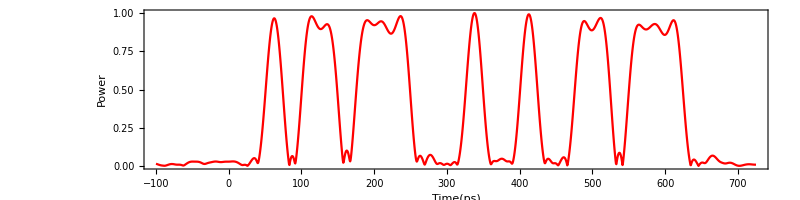

```mathematica
maxsig=Max[Table[{Abs[after[m]]},{m,1,25*bit+100,samp}]];
aftersig2=Table[{m,Abs[after[m]]/maxsig},{m,-100,25*bit+100,samp}];
ListLinePlot[aftersig2,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,PlotRange->{0,1},ImageSize->800]
```

## Eye Pattern

```mathematica
For[i=0.,i<=25*bit,i=i+samp,eyetime[i]=Mod[i,50]]
```

```mathematica
Print["Eye is ",(bit*25)/50]
```

Eye is 25/2

```mathematica
Table[eyetime[m],{m,0,25*bit,samp}];
```

```mathematica
eyebf=Table[{eyetime[m],nrzsig2[m+12.5]},{m,0,25*bit-12.5,samp}];
eyeaf=Table[{eyetime[m],Abs[after[m+12.5]]/maxsig},{m,0,25*bit-12.5,samp}];
```

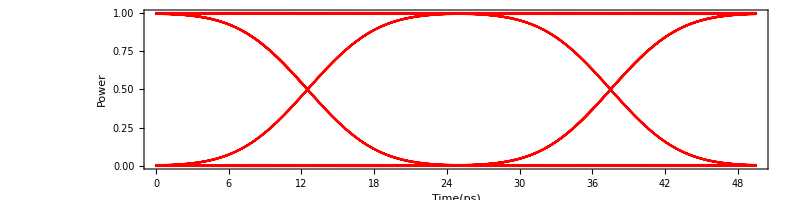

```mathematica
ListLinePlot[eyebf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

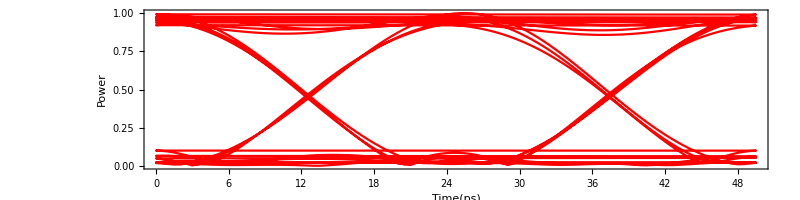

```mathematica
ListLinePlot[eyeaf,Frame->True,FrameLabel->{"Time(ps)","Power"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},AspectRatio->1/4,ImageSize->800]
```

## Bit Error Rate

```mathematica
For[m=22.5,m≤27.5,m=m+samp,For[i=m*2+1;j=1,i<= (bit*25-12.5)*1/samp,i=i+50*1/samp;j++,Subscript[list, m][j]=Part[eyeaf[[All,2]],i]]]
```

```mathematica
For[j=22.5;m=1;n=1;l0=0;l1=0,j≤27.5,j=j+samp,For[i=1,i≤(bit*25)/50,i++,
If[Subscript[list, j][i]>0.5,eye1[m]=Subscript[list, j][i];m++;l1=l1+1];
If[Subscript[list, j][i]<0.5,eye0[n]=Subscript[list, j][i];n++;l0=l0+1]]]
```

```mathematica
Print["1 is ",l1," point"]
Print["0 is ",l0," point"]
```

1 is 66 point

0 is 66 point

```mathematica
Table[eye1[m],{m,1,l1,1}];
Table[eye0[m],{m,1,l0,1}];
ave1=Sum[eye1[i],{i,1,l1}]/l1;
ave0=Sum[eye0[i],{i,1,l0}]/l0;
```

```mathematica
Print["Average of 1 is ",ave1]
Print["Average of 0 is ",ave0]
```

Average of 1 is 0.945041

Average of 0 is 0.0406386

```mathematica
disp1=√(Sum[(eye1[i]-ave1)^2,{i,1,l1}]/l1);
disp0=√(Sum[(eye0[i]-ave0)^2,{i,1,l0}]/l0);
```

```mathematica
Print["A Standard Deviation of 1 is ",disp1]
Print["A Standard Deviation of 0 is ",disp0]
```

A Standard Deviation of 1 is 0.0283

A Standard Deviation of 0 is 0.0213698

```mathematica
gauss1[x_]:=1/(√(2*Pi*disp1^2))*Exp[-1/2*((x-ave1)/disp1^2)^2];
gauss0[x_]:=1/(√(2*Pi*disp0^2))*Exp[-1/2*((x-ave0)/disp0^2)^2];
```

General::munfl: Exp[-696151.]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

General::munfl: Exp[-3955.55]は正規化された機械数として表すには小さすぎます．精度が失われる可能性があります．

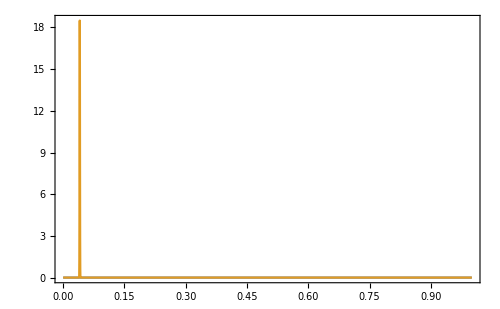

```mathematica
Plot[{gauss1[x],gauss0[x]},{x,0,1},PlotRange->All,Frame->True,ImageSize->500]
```

```mathematica
Q=(ave1-ave0)/(disp1+disp0);
Qdb=20Log10[Q];
Print["Q-factor is ",Q]
Print["Q-dB is ",Qdb," dB"]
```

Q-factor is 18.2083

Q-dB is 25.2054 dB

```mathematica
ber[x_]:=1/2*Erfc[x/(√2)];
Eyeopening=((ave1-disp1)-(ave0+disp0))/(ave1-ave0);
Print["Bit Error Rate is ",ber[Q]]
Print["Eye Opening is ",Eyeopening]
```

Bit Error Rate is 2.21917×10^-74

Eye Opening is 0.94508

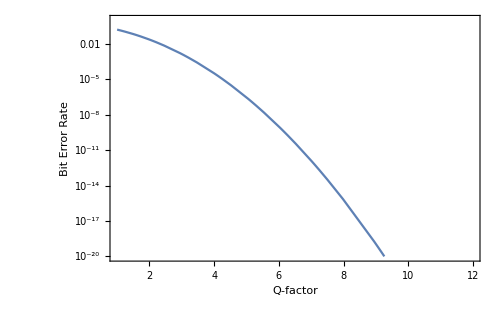

```mathematica
LogPlot[ber[z],{z,1,100},PlotRange->{{1,12},{10^-20,1}},Frame->True,FrameLabel->{"Q-factor","Bit Error Rate"},BaseStyle->{FontSize->20,Red,FontWeight->Bold},LabelStyle->{GrayLevel[0],Bold},ImageSize->500]
```